Note: In this problem set, expressions in green cells match corresponding expressions in the text answers.

```mathematica
Clear["Global`*"]
```

1 - 6 Fitting a straight line
Fit a straight line to the given points (x,y) by least squares. Show the details. Check your result by sketching the points and the line. Judge the goodness of fit.

1.  {0, 2}, {2, 0}, {3, -2}, {5, -3}

I like it that the following fit-finding functions provide the equations for the functions which are plotted. Fit is a least-squares function, which jibes with the imperative of the problem. As for IP, I couldn’t resist using it also. Goodness of fit seems acceptable.

```mathematica
Clear["Global`*"]
```

```mathematica
lis={{0,2},{2,0},{3,-2},{5,-3}}
```

{{0,2},{2,0},{3,-2},{5,-3}}

```mathematica
ip=InterpolatingPolynomial[lis,x]
```

2+(-1+(-1/3+1/6 (-3+x)) (-2+x)) x

```mathematica
p1=Plot[ip,{x,0,6},PlotStyle->Thickness[0.004],Epilog->{Red,PointSize[0.015],Point/@lis},ImageSize->250];
```

Demonstrating that the Fit function is actually using least squares,

```mathematica
line = Fit[lis, {1,x},x]
```

1.84615-1.03846 x

```mathematica
p2 = Plot[line,{x,0,6},PlotStyle->{Black,Thickness[0.004]},ImageSize->250];
```

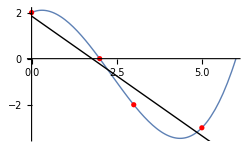

```mathematica
Show[p1,p2]
```

3.  {0, 1.8}, {1, 1.6}, {2, 1.1}, {3, 1.5}, {4, 2.3}

```mathematica
Clear["Global`*"]
```

```mathematica
lis={{0,1.8},{1,1.6},{2,1.1},{3,1.5},{4,2.3}}
```

{{0,1.8},{1,1.6},{2,1.1},{3,1.5},{4,2.3}}

```mathematica
ip=InterpolatingPolynomial[lis,x]
```

2.3+(-4+x) (0.125+(0.2375+(0.129167-0.0708333 (-1+x)) (-2+x)) x)

```mathematica
p1=Plot[ip,{x,0,6},PlotStyle->Thickness[0.004],Epilog->{Red,PointSize[0.015],Point/@lis},ImageSize->250];
```

```mathematica
line = Fit[lis, {1,x},x]
```

1.48+0.09 x

```mathematica
p2 = Plot[line,{x,0,6},PlotStyle->{Black,Thickness[0.004]},ImageSize->250];
```

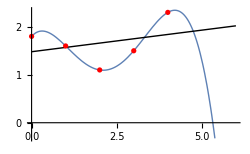

```mathematica
Show[p1,p2]
```

5.  Average Speed. Estimate the average speed v_av of a car traveling according to s = v · t  [km] (s = distance traveled, t [hr] = time) from {t,s} = {9,140}, {10,220}, {11,310}, {12,410}.

```mathematica
Clear["Global`*"]
```

```mathematica
lin={{9,140},{10,220},{11,310},{12,410}}
```

{{9,140},{10,220},{11,310},{12,410}}

Mathematica has an easy-to-use arc length function. I’m not using it this time, but it’s nice to know it’s there.

```mathematica
N[ArcLength[Line[lin]]]
```

270.017

```mathematica
lins = Fit[lin, {1,t},t]
```

-675.+90. t

From the points list it is clear that the vehicle traveled 80 km in first hr, then 90 km in second hr, then 100 km in third hr, obviously having an average speed of 90 km/hr.

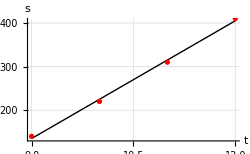

```mathematica
p1 = Plot[lins,{t,9,12},PlotStyle->{Black,Thickness[0.004]},ImageSize->250,AxesLabel->{t,s},PlotRange->All,GridLines->Automatic,Epilog->{Red,PointSize[0.015],Point/@lin}]
```

8 - 11 Fitting a quadratic parabola
Fit a parabola (7) to the points (x,y). Check by sketching.

9. {2, -3}, {3, 0}, {5, 1}, {6, 0}, {7, -2}

```mathematica
Clear["Global`*"]
```

```mathematica
dat={{2,-3},{3,0},{5,1},{6,0},{7,-2}}
```

{{2,-3},{3,0},{5,1},{6,0},{7,-2}}

The Fit function is checked out for performance in creating quadratic curves.

```mathematica
parabola = Fit[dat, {1,x,x^2}, x]
```

-11.3571+5.44643 x-0.589286 x^2

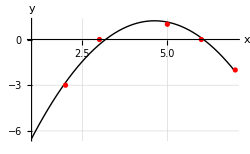

```mathematica
p1 = Plot[parabola,{x,1,7},PlotStyle->{Black,Thickness[0.004]},ImageSize->250,AxesLabel->{x,y},PlotRange->All,GridLines->Automatic,Epilog->{Red,PointSize[0.015],Point/@dat}]
```

11.  The data in problem 3. Plot the points, the line, and the parabola jointly. Compare and comment.

Interesting how little change is necessary to expand the plot to include both curves.

```mathematica
Clear["Global`*"]
```

```mathematica
lis={{0,1.8},{1,1.6},{2,1.1},{3,1.5},{4,2.3}}
```

{{0,1.8},{1,1.6},{2,1.1},{3,1.5},{4,2.3}}

```mathematica
line = Fit[lis, {1,x},x]
```

1.48+0.09 x

```mathematica
par= Fit[lis, {1,x, x^2},x]
```

1.89429-0.738571 x+0.207143 x^2

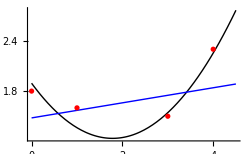

```mathematica
p2 = Plot[{par,line},{x,0,4.5},PlotStyle->{{Black,Thickness[0.004]},{Blue,Thickness[0.004]}},Epilog->{Red,PointSize[0.015],Point/@lis},ImageSize->250]
```

13.  Fit curves (2) and (7) and a cubic parabola by least squares to (x,y) = {-2,-30}, {-1,-4}, {0,4}, {1,4}, {2,22}, {3,68}. Graph these curves and the points on common axes. Comment on the goodness of fit.

```mathematica
Clear["Global`*"]
```

```mathematica
dat={{-2,-30},{-1,-4},{0,4},{1,4},{2,22},{3,68}}
```

{{-2,-30},{-1,-4},{0,4},{1,4},{2,22},{3,68}}

```mathematica
line = Fit[dat, {1,x},x]
```

2.55238+16.2286 x

```mathematica
parab = Fit[dat, {1,x,x^2},x]
```

-4.11429+13.7286 x+2.5 x^2

```mathematica
cubic = Fit[dat, {1,x,x^2,x^3},x]
```

2.73016+1.46561 x-1.77778 x^2+2.85185 x^3

```mathematica
backer =Fit[dat, {1,x,x^2,x^3,x^4,x^5},x]
```

4.-0.0666667 x-4.66667 x^2+4.33333 x^3+0.666667 x^4-0.266667 x^5

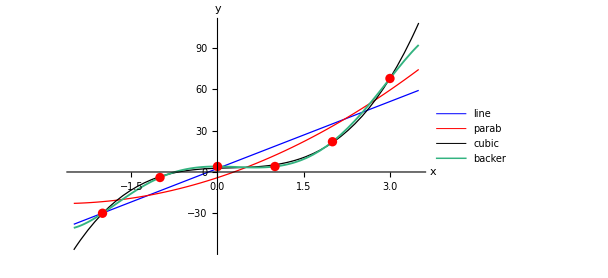

```mathematica
p1 = Plot[{line,parab,cubic,backer},{x,-2.5,3.5},PlotStyle->{{Blue,Thickness[0.002]},{Red,Thickness[0.002]},{Black,Thickness[0.002]},{RGBColor[0.2,0.7,0.5],Thickness[0.003]}},Epilog->{Red,PointSize[0.015],Point/@dat},ImageSize->450,AxesLabel->{x,y},PlotLegends->{"line","parab","cubic","backer"}]
```

As I learned when reading about splines, it takes a cubic to conform well to an arbitrary set of points. However, it seems that performance is limited. Here, x=0, x=1 and even x=2 do not quite fall on the curve. I tried to remedy by adding the function backer, which improves the conformance quite a bit, though at the cost of fifth order.

```mathematica
ip=InterpolatingPolynomial[dat,x]
```

-30+(2+x) (26+(1+x) (-9+(5/3+(2/3-4/15 (-2+x)) (-1+x)) x))

```mathematica
p3=Plot[ip,{x,-2.5,3.5}, PlotStyle->{LightRed,Thickness[0.01]},Epilog->{Red,PointSize[0.015],Point/@dat}];
p4=Plot[backer,{x,-2.5,3.5},PlotStyle->{Thickness[0.002]}];
```

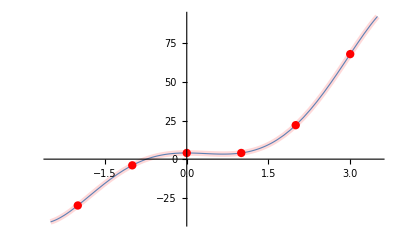

```mathematica
Show[p3,p4]
```

InterpolatingPolynomial also deems it necessary to use 5th order. And it looks like the same curve that Fit used for making ‘backer’ conform to this set of points.